```mathematica
NotebookDirectory[]
```

/home/freek/Documents/temp/Introgression/Matlab/data/

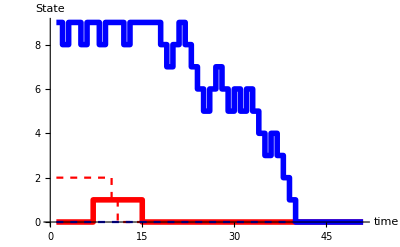

/home/freek/Documents/temp/Introgression/Matlab/data/Realization1.eps

```mathematica
data1=Import["/home/freek/Documents/temp/Introgression/Matlab/data/Realization1.csv"];
plot1=ListStepPlot[(Transpose[data1]-1)[[;;,1;;50]],PlotStyle->{{Red,Thickness[0.010]},{Red,Dashed},{Blue,Thickness[0.01]},{Blue,Dashed}},AxesLabel->{"time","State"}]
Export["/home/freek/Documents/temp/Introgression/Matlab/data/Realization1.eps",plot1]
```

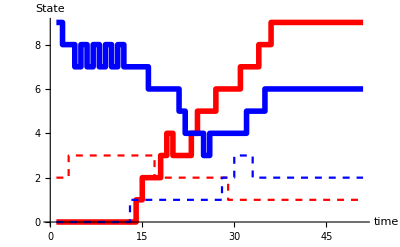

```mathematica
data2=Import["/home/freek/Documents/temp/Introgression/Matlab/data/Realization2.csv"];
plot2=ListStepPlot[(Transpose[data2]-1)[[;;,1;;50]],PlotStyle->{{Red,Thickness[0.010]},{Red,Dashed},{Blue,Thickness[0.01]},{Blue,Dashed}},AxesLabel->{"time","State"}]
Export["/home/freek/Documents/temp/Introgression/Matlab/data/Realization2.eps",plot2];
```

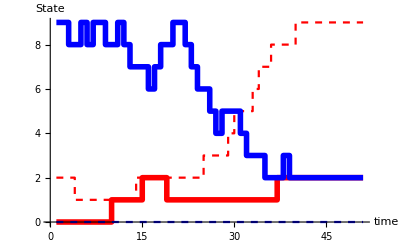

```mathematica
data3=Import["/home/freek/Documents/temp/Introgression/Matlab/data/Realization3.csv"];
plot3=ListStepPlot[(Transpose[data3]-1)[[;;,1;;50]],PlotStyle->{{Red,Thickness[0.010]},{Red,Dashed},{Blue,Thickness[0.01]},{Blue,Dashed}},AxesLabel->{"time","State"}]
Export["/home/freek/Documents/temp/Introgression/Matlab/data/Realization3.eps",plot3];
```

```mathematica
Legend=LineLegend[{{Red,Thickness[0.010]},{Red,Dashed},{Blue,Thickness[0.01]},{Blue,Dashed},0},{"AB","Ab","aB","ab"}];
```

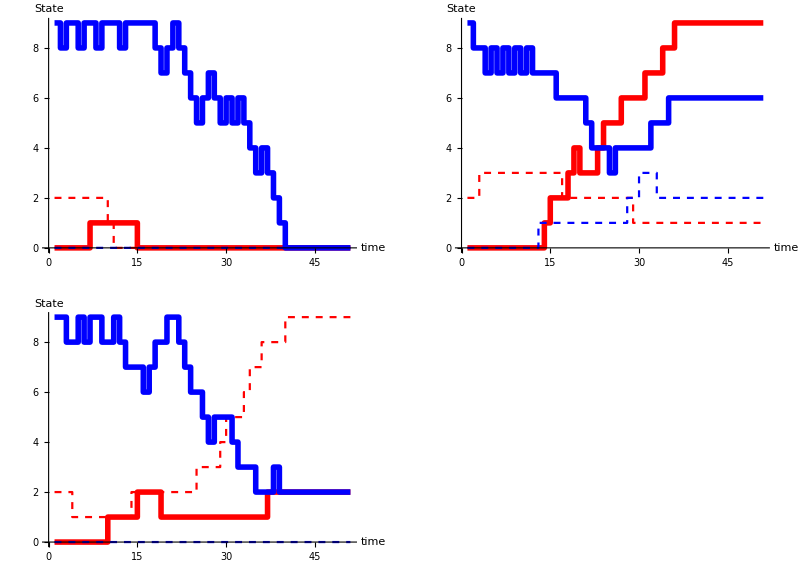

```mathematica
gridplot=GraphicsGrid[{{plot1,plot2},{plot3,Legend}}]
```

```mathematica
Export["/home/freek/Documents/temp/Introgression/Matlab/data/gridplot.eps",gridplot]
```

/home/freek/Documents/temp/Introgression/Matlab/data/gridplot.eps